# GWPEnsemble and EnsembleTrajectoryTools

Jeremy B. Maddox

Department of Chemistry and Biochemistry
Western Kentucky University
Bowling Green, KY 42101-1079
Email: jeremy.maddox@wku.edu

The GWPEnsemble package generates structured coordinate and phase-space point ensembles from GWPObject instances across the 1D, SS1D, MC1D, and 2D wavepacket engines. These ensembles provide initial condition grids and trajectory markers for quantum hydrodynamic (Bohmian) propagation, semiclassical phase-space sampling, and Monte Carlo integration.

## Loading the package

First, load the base GWPTools package alongside the GWPEnsemble extension:

```mathematica
Quit[]
```

```mathematica
PacletDirectoryLoad["/Users/jrm82302/maddox/Projects/Mathematica/GWPTools"];
PacletDirectoryLoad["/Users/jrm82302/maddox/Projects/Mathematica/NumericalTools"];
Needs["MaddoxScience`GWPTools`"]
Needs["MaddoxScience`GWPTools`GWPEngineSS1D`"]
Needs["MaddoxScience`GWPTools`GWPEngineMC1D`"]
Needs["MaddoxScience`GWPTools`GWPEngine2D`"]
Needs["MaddoxScience`GWPTools`GWPEnsemble`"]
Needs["MaddoxScience`GWPTools`GWPHydrodynamics`"]
Needs["MaddoxScience`GWPTools`GWPPhaseSpace`"]
Needs["MaddoxScience`GWPTools`GWPNumerical`"]
Needs["MaddoxScience`NumericalTools`EnsembleTrajectoryTools`"]
```

```mathematica
GWP["Types"]
```

{1D,SS1D,MC1D,2D}

## Single GWP Examples (1D)

We begin by initializing a default stationary wavepacket (α_0=1/4, x_0=0, which has position uncertainty σ_x=Δ x=1):

```mathematica
obj=GWP["1D"][];
```

Calling GWPEnsemble[obj] with no options triggers the default settings “SamplingMethod” → Automatic and “Grid”→ Automatic. For a 1D wavepacket, Automatic routes to “UniformC” (uniform cumulative distribution / quantile sampling) and generates a 100-point grid evaluated at the probability midpoints

c_k=(2k-1)/(2N)∈(0,1)

via the analytical inverse cumulative distribution function (GWP1DXC)

```mathematica
(*Default:100 equal-probability quantile points ("UniformC")*)
xdatDefault=GWPEnsemble[obj];
Length[xdatDefault]
Short[xdatDefault]
```

100

{-√2 InverseErf[99/100],-√2 InverseErf[97/100],«96»,√2 InverseErf[97/100],√2 InverseErf[99/100]}

Selecting “SamplingMethod” → “UniformX” generates a uniformly spaced Cartesian coordinate grid centered around the wavepacket’s expectation value x_t. The “Grid” option accepts three formats to control the number of grid points N and the spatial domain bounds:  

“Grid” → N (or Automatic for N=100): Subdivides the default ±4 σ_x interval [x_t-4 σ_x,x+4 σ_x] into N evenly spaced points.   

“Grid” → {N, “3Sigma”}: Subdivides the narrower ±3 σ_x interval [x_t-3 σ_x,x_t+3 σ_x] into N points.   

“Grid” → {N, {xMin, xMax}}: Subdivides a user-specified coordinate window [x_min,x_max] into N points.

```mathematica
(*10 points across the default+/-4*Sigma window[-4,4]*)xdatX1=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->10]

(*10 points across the+/-3*Sigma window[-3,3]*)
xdatX2=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->{10,"3Sigma"}]

(*10 points across an explicit coordinate window[0,2]*)
xdatX3=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->{10,{0,2}}]
```

{-4,-28/9,-20/9,-4/3,-4/9,4/9,4/3,20/9,28/9,4}

{-3,-7/3,-5/3,-1,-1/3,1/3,1,5/3,7/3,3}

{0,2/9,4/9,2/3,8/9,10/9,4/3,14/9,16/9,2}

Selecting “SamplingMethod” → “UniformC” places grid points at equal probability intervals along the cumulative distribution function

C(x)=∫_(-∞)^x ρ(x')ⅆ x'∈(0,1)

naturally concentrating points near the peak of the probability density and spreading them out in the tails (ideal for equal-weight Bohmian trajectory ensembles):   

“Grid” → N: Evaluates the inverse CDF at the N bin midpoints c_k=1/2N,3/2N,…,1-1/2N (avoiding the divergent endpoints at c=0 and c=1).   

“Grid” → {N, {cMin, cMax}}: Subdivides the cumulative probability window [c_min,c_max]⊂(0,1) into N points including the endpoints.

```mathematica
(*10 exact quantile points across the full distribution*)xdatC1=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->10]

(*10 exact quantile points restricted to the cumulative probability quartile[1/2,3/4]*)
xdatC2=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->{10,{1/2,3/4}}]
```

{-√2 InverseErf[9/10],-√2 InverseErf[7/10],-√2 InverseErf[1/2],-√2 InverseErf[3/10],-√2 InverseErf[1/10],√2 InverseErf[1/10],√2 InverseErf[3/10],√2 InverseErf[1/2],√2 InverseErf[7/10],√2 InverseErf[9/10]}

{0,√2 InverseErf[1/18],√2 InverseErf[1/9],√2 InverseErf[1/6],√2 InverseErf[2/9],√2 InverseErf[5/18],√2 InverseErf[1/3],√2 InverseErf[7/18],√2 InverseErf[4/9],√2 InverseErf[1/2]}

GWPEnsemble provides two distinct random sampling modes for 1D wavepackets:   

“SamplingMethod” → “Random”: Draws N sorted variates directly from the analytical unbounded Gaussian distribution NormalDistribution[RX, ux] over (-∞,∞). (Note that “Random” only reads the point count N from “Grid” and ignores spatial bound specifications.)   

“SamplingMethod” → “RandomDensity”: Constructs a numerical ProbabilityDistribution from the wavepacket density GWP1DRHOX truncated and normalized over a bounded spatial domain (±4 σ_x by default, “3Sigma”, or an explicit {xMin, xMax} window).

```mathematica
(*10 sorted random variates from the full unbounded normal distribution*)xdatR1=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->10]

(*10 sorted random variates restricted to the+/-3*Sigma window[-3,3]*)
xdatRD1=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{10,"3Sigma"}]

(*10 sorted random variates restricted to the positive spatial window[0,2]*)
xdatRD2=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{10,{0,2}}]
```

{-1.19112,-1.03523,-0.421126,-0.294261,-0.289226,-0.174919,0.386439,0.502407,0.617018,1.48115}

{-0.892904,-0.773811,-0.334916,-0.0339347,0.599164,0.956518,1.07137,1.21735,1.54443,1.70878}

{0.00375821,0.231522,0.231867,0.696145,1.08453,1.19284,1.21483,1.28742,1.64583,1.97604}

By default (WorkingPrecision → Automatic), “Random” and “RandomDensity” generate machine-precision floating-point numbers, whereas exact methods (“UniformX” and “UniformC”) preserve exact symbolic expressions when the underlying wavepacket parameters are exact. Passing an explicit WorkingPrecision option overrides this default across all sampling methods—generating arbitrary-precision random variates or directly evaluating exact symbolic grids to the requested number of digits:

```mathematica
(*Arbitrary-precision random sampling (25 digits)*)xdatR25=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->5,WorkingPrecision->25]

xdatRD25=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{5,{0,2}},WorkingPrecision->25]

(*Evaluating an exact symbolic quantile grid ("UniformC") directly to 25-digit precision*)
xdatC25=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->5,WorkingPrecision->25]
```

{-2.279185080341776433452662,-0.6331975018575078055850196,0.02314369590061833901078602,0.4810664319694441068842855,0.8107019358910666534049785}

{0.1199490847036254552370149,0.1703905648816325949962733,0.4558119859692523551736979,0.7213664844302185760733863,0.8009445437926750776485998}

{-1.281551565544600466965103,-0.5244005127080407840382893,0,0.5244005127080407840382893,1.281551565544600466965103}

We can visually compare the point distributions of “UniformX”, “UniformC”, and “Random” (for N=25) against the underlying Gaussian probability density ρ(x):

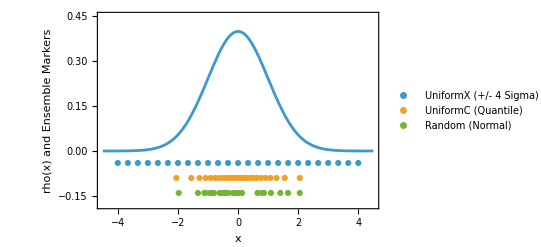

```mathematica
ensX=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->25];
ensC=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->25];
ensR=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->25];

Show[Plot[obj["RHOX"][x],{x,-4.5,4.5},PlotRange->{-0.18,0.45},Frame->True,FrameLabel->{"x","rho(x) and Ensemble Markers"},BaseStyle->FontSize->12],ListPlot[{Thread[{ensX,-0.04}],Thread[{ensC,-0.09}],Thread[{ensR,-0.14}]},PlotLegends->{"UniformX (+/- 4 Sigma)","UniformC (Quantile)","Random (Normal)"}]]
```

When a GWPObject is initialized with a “Potential” model, passing the “Time” → t0 option (default 0) instructs GWPEnsemble to propagate the wavepacket parameters to time t_0 prior to generating the coordinate ensemble.   Below, we initialize a squeezed, displaced wavepacket (α_0=1/2, x_0=-2) in a harmonic oscillator (“Potential” → “HO”) and sample its 15-point quantile ensemble at t=0, t=π/2 (origin crossing with compressed width), and t=π (right turning point):

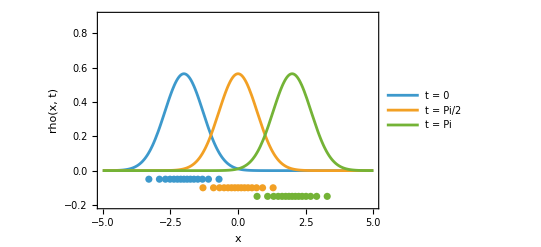

```mathematica
objDyn=GWP["1D"][1/2,-2,"Potential"->"HO"];

ensT0=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->0];
ensT1=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->Pi/2];
ensT2=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->Pi];

Show[Plot[{objDyn["RHOX"][x,0],objDyn["RHOX"][x,Pi/2],objDyn["RHOX"][x,Pi]},{x,-5,5},PlotRange->{-0.2,0.9},Frame->True,FrameLabel->{"x","rho(x, t)"},PlotLegends->{"t = 0","t = Pi/2","t = Pi"},BaseStyle->FontSize->12],ListPlot[{Thread[{ensT0,-0.05}],Thread[{ensT1,-0.10}],Thread[{ensT2,-0.15}]}]]
```

## Superposition Examples (SS1D and MC1D)

For two-state (SS1D) and multi-component (MC1D) superpositions, quantum interference between overlapping Gaussian branches produces oscillatory nodes and fringes in the probability density ρ(x,t). Consequently, the cumulative distribution function C(x) cannot be inverted analytically in closed form.  Both SS1D and MC1D share an identical GWPEnsemble interface with three sampling methods:

“UniformX” (or “Cartesian” / Automatic): Subdivides the composite ±4 σ_x bounding box [min_k (x_k-4 σ_k),max_k (x_k+4 σ_k)] (or a user-supplied {N, {xMin, xMax}} window) into N evenly spaced points.  

“InverseC” (Numerical Quantile Root-Finding): Solves C(x_k)=c_k sequentially across the quantile grid using FindRoot supplied with the exact analytical Jacobian ∂_x C(x)=ρ(x). Any standard FindRoot options (such as WorkingPrecision, AccuracyGoal, or MaxIterations) may be passed directly into GWPEnsemble.   

“RandomDensity” (Rejection Sampling): Generates N sorted variates via von Neumann rejection sampling under a bounding envelope of the interfering probability density.

Here we initialize an antisymmetric two-Gaussian superposition (“C” → -1) with overlapping branches centered at x_0=±1/2 (α_0=1), creating a destructive interference node at x=0. Comparing “UniformX”, “InverseC”, and “RandomDensity” demonstrates how both “InverseC” and “RandomDensity” automatically evacuate the destructive node at the origin and cluster trajectories inside the two constructive interference lobes:

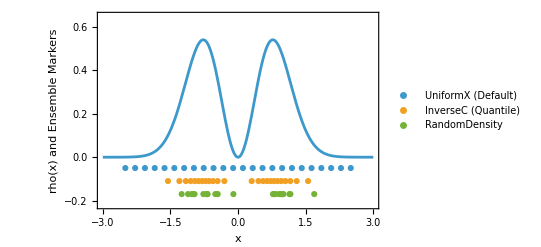

```mathematica
(*Antisymmetric overlapping two-state superposition with a node at x=0*)
objSS=GWP["SS1D"][{1,1},{-1/2,1/2},"C"->-1];
ensSSX=GWPEnsemble[objSS,"SamplingMethod"->"UniformX","Grid"->24];
ensSSC=GWPEnsemble[objSS,"SamplingMethod"->"InverseC","Grid"->24];
ensSSRD=GWPEnsemble[objSS,"SamplingMethod"->"RandomDensity","Grid"->24];

Show[Plot[objSS["RHOX"][x],{x,-3,3},PlotRange->{-0.22,0.65},Frame->True,FrameLabel->{"x","rho(x) and Ensemble Markers"},BaseStyle->FontSize->12],ListPlot[{Thread[{ensSSX,-0.05}],Thread[{ensSSC,-0.11}],Thread[{ensSSRD,-0.17}]},PlotLegends->{"UniformX (Default)","InverseC (Quantile)","RandomDensity"}]]
```

In this dynamic MC1D example, three Gaussian wavepackets (α_0=1) initialized at x_0∈{-3,0,3} in a harmonic oscillator (“Potential” → “HO”) are sampled via “InverseC” at t=0 (three well-separated Gaussian peaks) and at the half-period focal collision t=π/2 (where all three branches cross at the origin to form high-frequency three-beam interference fringes):

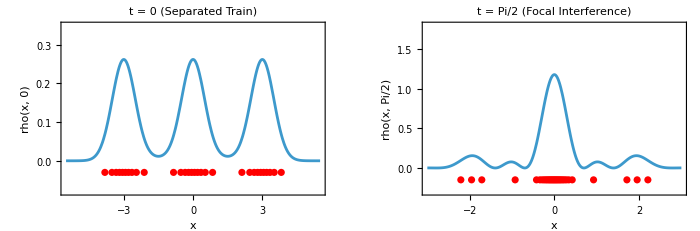

```mathematica
objMC=GWP["MC1D"][{1,1,1},{-3,0,3},"C"->{1,1,1},"Potential"->"HO"];

(*30 quantile points at t=0 (separated lobes) vs t=Pi/2 (focal interference)*)
ensMC0=GWPEnsemble[objMC,"SamplingMethod"->"InverseC","Grid"->30,"Time"->0];
ensMCT=GWPEnsemble[objMC,"SamplingMethod"->"InverseC","Grid"->30,"Time"->Pi/2];

GraphicsRow[{Show[Plot[objMC["RHOX"][x,0],{x,-5.5,5.5},PlotRange->{-0.08,0.35},Frame->True,FrameLabel->{"x","rho(x, 0)"},PlotLabel->"t = 0 (Separated Train)"],ListPlot[Thread[{ensMC0,-0.03}],PlotStyle->Red]],Show[Plot[objMC["RHOX"][x,Pi/2],{x,-3,3},PlotRange->{-0.3,1.8},Frame->True,FrameLabel->{"x","rho(x, Pi/2)"},PlotLabel->"t = Pi/2 (Focal Interference)"],ListPlot[Thread[{ensMCT,-0.15}],PlotStyle->Red]]},ImageSize->700]
```

## Single GWP Examples (2D)

For two-dimensional wavepackets (“2D”), GWPEnsemble generates lists of coordinate pairs {{x1, y1}, {x2, y2}, ...} adapted to the position center μ=(x_t,y_t)^T and 2×2 spatial covariance matrix Σ_r of the wavepacket.

In GWP2DENSEMBLE, the “Grid” option accepts three flexible formats:   

“Grid” → Automatic: Defaults to a 20×20 mesh (400 total points).   

“Grid”→ N (single integer): Sets the total point count to N for random methods (“Random” and “RandomDensity”), or constructs an approximately square √N×√N mesh for structured grid methods.   

“Grid” → {nx, ny} or {nx, ny, {{xMin, xMax}, {yMin, yMax}}}: Explicitly specifies the grid dimensions n_x×n_y (or n_r×n_θ radial shells and angular rays for “PolarC”), along with optional custom bounding intervals for “Cartesian” and “RandomDensity”.

Five “SamplingMethod” geometries are available for 2D wavepackets:   

“Cartesian” (or “UniformX” / Automatic): Forms a rectangular n_x×n_y outer-product grid across [x_t-4 σ_x,x_t+4 σ_x]×[y_t-4 σ_y,y_t+4 σ_y] (or custom bounds).   

“AffineC” (Cholesky Quantile Mesh): For a correlated 2D Gaussian wavepacket, the spatial probability density ρ(x,y) does not factorize along the laboratory x and y axes, meaning independent 1D quantile grids cannot capture its tilted covariance ellipse. To construct an exact equal-probability mesh without numerical root-finding, “AffineC” first generates an uncorrelated n_x×n_y canonical quantile grid z=(z_x,z_y)^T for a 2D standard normal distribution (μ_z=(0,0)^T, Σ_z=I_2) by evaluating the 1D inverse cumulative distribution function z_k=√2 erf^-1(2 c_k-1) at the probability midpoints c_k∈(0,1) along each axis. Next, it computes the lower-triangular Cholesky decomposition L of the wavepacket’s 2×2 spatial covariance matrix Σ_r=L L^T and applies the affine transformation r=μ+L z to every canonical point z. Geometrically, L scales and shears the rectangular unit-normal quantile mesh so that it aligns with the principal axes and correlation tilt of the physical wavepacket centered at μ=(x_t,y_t)^T.   

“PolarC” (Radial-Angular Quantile Shells): Rather than warping a rectangular grid, “PolarC” samples the 2D Gaussian probability distribution in canonical polar quantile coordinates (c_r,c_θ)∈[0,1)×[0,1). For a grid specification of n_r radial shells and n_θ angular rays, the method places radial cumulative probability coordinates at uniform intervals (c_(r,i)=i/(n_r+1), i=1,…,n_r) and distributes n_θ angular phase coordinates uniformly around each shell (c_(θ,j)=j/n_θ, j=0,…,n_θ-1).  When “Structure” → “Staggered” (the default) is active, odd-numbered radial shells are shifted in angular phase by half a ray spacing (Δc_θ=1/2 n_θ) to create a triangulated packing, whereas “Aligned” keeps all points along fixed radial spokes. If “IncludeCore” → True (the default), the origin point (c_r,c_θ)=(0,0) is prepended to the ensemble. Finally, each (c_r,c_θ) pair is mapped through the backend 2D polar inverse cumulative distribution (GWP2DXC), which converts (c_r,c_θ) into canonical polar coordinates (ρ=√(-2ln(1-c_r)), ϕ=2π c_θ) and transforms them onto concentric constant-probability ellipses aligned with the wavepacket’s covariance matrix Σ_r and center μ. 


“Random”: Draws N=n_x n_y variates directly from the analytical MultinormalDistribution[mu, sigma].   

“RandomDensity”: Draws N variates via 2D numerical rejection sampling over the bounding box.

To highlight how the structured quantile methods adapt to anisotropic squeezing and inter-mode correlation, we construct a 2D wavepacket with a non-diagonal shape matrix centered at r_0=(1,-1):

```mathematica
(*Anisotropic,correlated 2D GWP tilted in the xy-plane*)
obj2D=GWP["2D"][{{1,3/5},{3/5,1/2}},{1,-1}];

ptsCart=GWPEnsemble[obj2D,"SamplingMethod"->"Cartesian","Grid"->{12,12}];
ptsAffine=GWPEnsemble[obj2D,"SamplingMethod"->"AffineC","Grid"->{12,12}];
ptsPolar=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{6,24}];
ptsRand=GWPEnsemble[obj2D,"SamplingMethod"->"Random","Grid"->144];
```

Visualizing all four 144-point ensembles superimposed on the contour plot of the 2D probability density ρ(x,y) illustrates how “AffineC” and “PolarC” shear and rotate automatically with the covariance ellipse, whereas “Cartesian” remains locked to the laboratory axes:

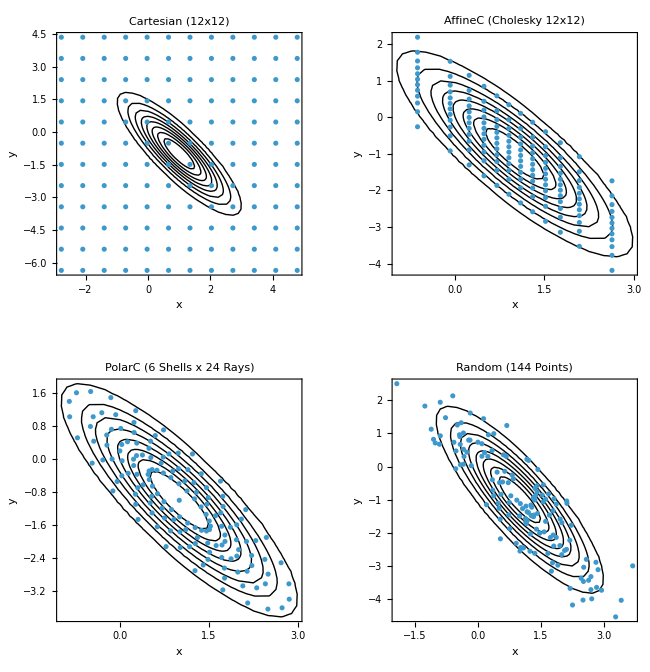

```mathematica
bgContour=ContourPlot[obj2D["RHOX"][x,y],{x,-2.5,4.5},{y,-5,3},PlotRange->All,Contours->8,ContourShading->None,ContourStyle->Thin,Frame->True,FrameLabel->{"x","y"}];

GraphicsGrid[{{Show[bgContour,ListPlot[ptsCart],PlotLabel->"Cartesian (12x12)"],Show[bgContour,ListPlot[ptsAffine],PlotLabel->"AffineC (Cholesky 12x12)"]},{Show[bgContour,ListPlot[ptsPolar],PlotLabel->"PolarC (6 Shells x 24 Rays)"],Show[bgContour,ListPlot[ptsRand],PlotLabel->"Random (144 Points)"]}},ImageSize->650]
```

The “PolarC” method supports two specialized layout options that control the arrangement of points across the concentric probability shells:   

“Structure” → “Staggered” (default) vs. “Aligned”: “Staggered” alternates the angular phase of adjacent radial shells by half a ray spacing (Δθ/2), producing a triangulated packing, whereas “Aligned” places points along radial spokes at fixed angles.   

“IncludeCore” → True (default) vs. False: Controls whether the wavepacket center μ=(x_t,y_t)^T (c_r=0) is prepended as a core point at the center of the innermost ring.

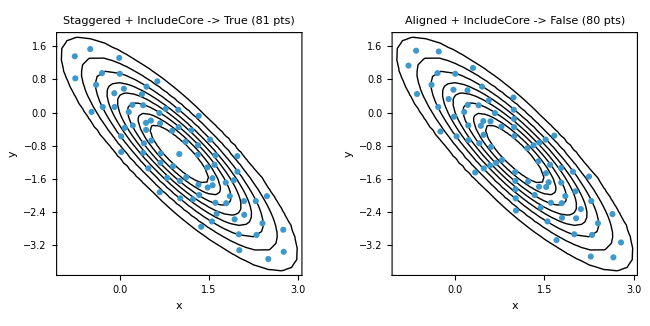

```mathematica
(*Compare Staggered (with core) vs.Aligned (without core) PolarC ensembles*)polarStaggered=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{5,16},"Structure"->"Staggered","IncludeCore"->True];

polarAligned=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{5,16},"Structure"->"Aligned","IncludeCore"->False];

GraphicsRow[{Show[bgContour,ListPlot[polarStaggered],PlotLabel->"Staggered + IncludeCore -> True (81 pts)"],Show[bgContour,ListPlot[polarAligned],PlotLabel->"Aligned + IncludeCore -> False (80 pts)"]},ImageSize->650]
```

## Ensemble Trajectory Tools

### 1D Squeezed & Displaced Harmonic Oscillator (Affine Breathing + Oscillation)

A single 1D Gaussian wavepacket displaced from equilibrium with an initial width narrower than the ground state exhibits classical center-of-mass sloshing combined with quantum width breathing at 2ω. Because the single-Gaussian Bohmian velocity field is strictly linear in x, the quantile trajectories form a non-crossing affine fan that expands and contracts in lockstep with the analytical standard deviation envelope.

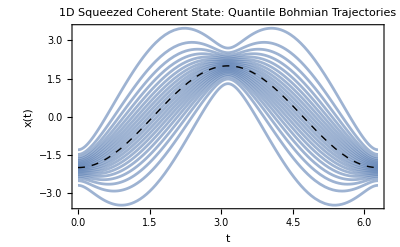

```mathematica
(*Displaced (r0=-2) and squeezed (a0=2) 1D harmonic oscillator*)
obj1D=GWP["1D"][2,-2,0,"Potential"->"HO"];
(*Sample 21 equiquantile initial positions via UniformC*)
x0=GWPEnsemble[obj1D,"SamplingMethod"->"UniformC","Grid"->21,"Time"->0];
(*Propagate 1st-order Bohmian trajectories over one full period[0,2 Pi]*)
sol1D=EnsembleSolve[x0,Function[{x,t},obj1D["VX"][x,t]],{t,0,2 Pi}];
parsed1D=EnsembleParse[x0,sol1D];
traj1D=EnsembleFormat[parsed1D,"X0DAT"];
(*Plot trajectories alongside the classical center RX(t)*)
Show[
ListLinePlot[traj1D,PlotStyle->Directive[Opacity[0.6],ColorData[97,1]],Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"1D Squeezed Coherent State: Quantile Bohmian Trajectories"],Plot[obj1D["RX"][t],{t,0,2 Pi},PlotStyle->{Black,Dashed,Thick}]]
```

### 2D Anisotropic Coupled Oscillator (Lissajous Swirl & Phase-Space Vorticity)

Using “SamplingMethod”→ “PolarC” on a 2D Gaussian wavepacket with initial off-diagonal correlation (α_(x y)!=0) and initial transverse momentum shows how EnsembleFormat extracts both 2D planar orbits and 1D coordinate projections.

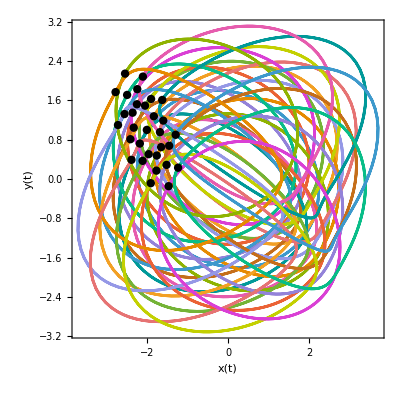

```mathematica
(*1. Correlated 2D Gaussian in an isotropic harmonic trap*)obj2D=GWP["2D"][{{3/2,1/2},{1/2,2/3}},{-2,1},{1,3/2},"Potential"->"HO"];
(*2. Sample 3 radial shells x 10 angular spokes=30 trajectories*)
xy0=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{3,10},"Time"->0];
(*3. Propagate 2D Bohmian velocity field*)
sol2D=EnsembleSolve[xy0,Function[{xy,t},Transpose@obj2D["VX"][xy[[All,1]],xy[[All,2]],t]],{t,0,2*2 Pi}];
parsed2D=EnsembleParse[xy0,sol2D];
(*4. Extract planar (x,y) trajectories and 1D x(t),y(t) projections*)
trajXY=EnsembleFormat[parsed2D,"X0DAT"];
trajX=EnsembleFormat[parsed2D,"X0DAT","Component"->1];
trajY=EnsembleFormat[parsed2D,"X0DAT","Component"->2];

GraphicsRow[{ListLinePlot[trajXY,AspectRatio->1,Frame->True,FrameLabel->{"x(t)","y(t)"},Epilog->{PointSize[0.015],Black,Point[xy0]}],
GraphicsColumn[{
ListLinePlot[trajX,Frame->True,FrameLabel->{"t","x(t)"},PlotRange->{-4,4}],
ListLinePlot[trajY,Frame->True,FrameLabel->{"t","y(t)"},PlotRange->{-4,4}]
}]
},ImageSize->750]
```

```mathematica
ListLinePlot3D[Partition[Flatten@Transpose@{parsed2D["TDAT"],#},3]&/@trajXY,BoxRatios->{3,1,1},PlotStyle->Directive[ColorData[97,1],Thin],AxesLabel->{"time","x(t)","y(t)"}]
```

-Graphics3D-

### Laser-Driven “Schrödinger’s Cat” Superposition (MC1D + Chirped Pulse)

A two-packet MC1D superposition starts separated in a harmonic trap (x_0={-2.5,2.5}) and is hit by an ultrashort Gaussian-envelope laser pulse

V_1(t)=E_0 ⅇ^(-(t-t_0)^2/τ^2)cos(ω_L t)

The trajectories exhibit sharp non-crossing topological bounces inside the interference fringes at the center of the trap while the entire interference pattern is shaken by the laser field.

```mathematica
(*1. Define a Gaussian-envelope oscillating laser pulse (dipole force v1[t])*)
GWPClearCache["Quiet"];
Clear[v0Pulse,v1Pulse,v2Pulse]
v0Pulse[t_]:=0;
v1Pulse[t_]:=2.5*Exp[-(t-Pi)^2/0.8^2]*Cos[4 t];
v2Pulse[t_]:=1; (*Harmonic confinement omega=1*)

(*2. Build a 2-state Cat superposition driven by the numerical pulse over[0,2 Pi]*)
objCat=GWP["MC1D"][{1,1},{-5/2,5/2},{0,0},"C"->{1,1},"Potential"->{"Numerical",v0Pulse,v1Pulse,v2Pulse,0,2 Pi}];

(*3. Sample 30 quantile trajectories across the bimodal initial density*)
x0Cat=GWPEnsemble[objCat,"SamplingMethod"->"InverseC","Grid"->30,"Time"->0];

(*4. Propagate trajectories through the laser-driven interference fringes*)
solCat=EnsembleSolve[x0Cat,Function[{x,t},objCat["VX"][x,t]],{t,0,2 Pi},MaxStepSize->0.02];

parsedCat=EnsembleParse[x0Cat,solCat];
trajCat=EnsembleFormat[parsedCat,"X0DAT"];
```

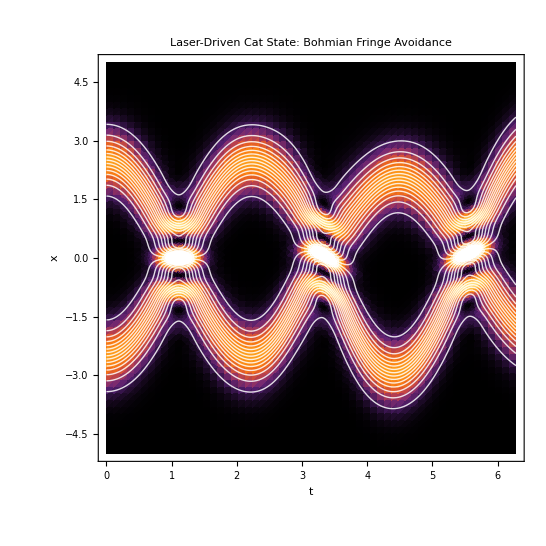

```mathematica
(*5. Overlay Bohmian trajectories on top of a DensityPlot of rho(x,t)*)
Show[DensityPlot[objCat["RHOX"][x,t],{t,0,2 Pi},{x,-5,5},PlotPoints->60,ColorFunction->"SunsetColors",FrameLabel->{"t","x"}],ListLinePlot[trajCat,PlotStyle->Directive[White,Opacity[0.85],Thin]],PlotLabel->"Laser-Driven Cat State: Bohmian Fringe Avoidance"]
```

### Parametric Resonance & Kapitza Pendulum in a 1D Paul Trap (MC1D / SS1D)

In an RF Paul trap, the quadratic curvature

V_2(t)=u_DC+u_AC cos(Ω t)

oscillates rapidly in time, governed by the Mathieu equation. A 3-packet superposition (MC1D) inside a modulated Paul trap exhibits rapid micromotion ripples superimposed on slow secular macromotion, while interference nodes weave between the micromotion oscillations.

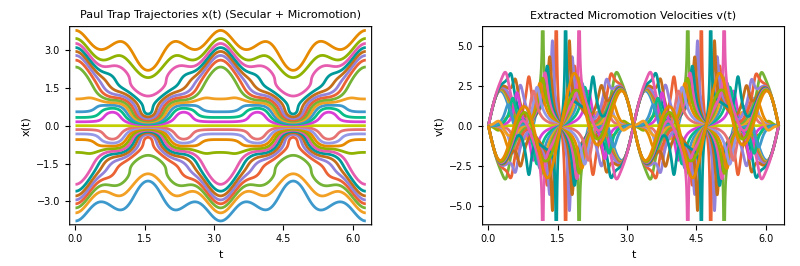

```mathematica
(*1. Paul trap curvature:DC confinement+high-frequency AC micromotion drive*)
GWPClearCache["Quiet"];
Clear[v0Paul,v1Paul,v2Paul]
v0Paul[t_]:=0;
v1Paul[t_]:=0;
v2Paul[t_]:=0.4+1.8*Cos[6 t]; (*Mathieu stability regime*)

(*2. 3-state superposition in the Paul trap*)
objPaul=GWP["MC1D"][{1,1,1},{-3,0,3},{0,0,0},"C"->{1,1,1},"Potential"->{"Numerical",v0Paul,v1Paul,v2Paul,0,2 Pi}];

(*3. Sample 25 quantile trajectories*)
x0Paul=GWPEnsemble[objPaul,"SamplingMethod"->"InverseC","Grid"->25,"Time"->0];

solPaul=EnsembleSolve[x0Paul,Function[{x,t},objPaul["VX"][x,t]],{t,0,2 Pi},MaxStepSize->0.02];

parsedPaul=EnsembleParse[x0Paul,solPaul];
trajPaul=EnsembleFormat[parsedPaul,"X0DAT"];
velPaul=EnsembleFormat[parsedPaul,"X1DAT"]; (*Extract exact micromotion velocities!*)

GraphicsRow[{ListLinePlot[trajPaul,Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Paul Trap Trajectories x(t) (Secular + Micromotion)"],ListLinePlot[velPaul,Frame->True,FrameLabel->{"t","v(t)"},PlotLabel->"Extracted Micromotion Velocities v(t)"]},ImageSize->800]
```

```mathematica
Dimensions[trajPaul]
```

{25,1578,2}

```mathematica
psdat=Table[Transpose@{trajPaul[[i,All,2]],velPaul[[i,All,2]]},{i,25}];
```

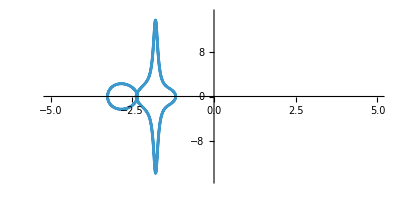

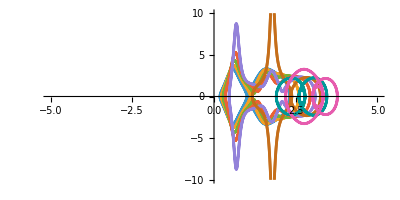

```mathematica
ListLinePlot[psdat[[3]],PlotRange->{{-5,5},{-15,15}},AspectRatio->1/2]
ListLinePlot[psdat[[-8;;-1]],PlotRange->{{-5,5},{-10,10}},AspectRatio->1/2]
```

```mathematica
velPaul[[1]]
```

{{0.,-7.52473×10^-22},{0.0000738487,0.00099767},{0.000147697,0.00199534},{0.000295395,0.00399067},{0.000443092,0.00598601},{0.000590789,0.00798133},{0.00206776,0.0279339},{0.00354474,0.047884},{0.00502171,0.0678299},{0.011043,0.149064},{0.0151683,0.204597},{0.0192935,0.259988},{0.0227212,0.305877},{0.0261488,0.351619},{0.0295765,0.397192},{0.0347377,0.465449},{0.0398989,0.533201},{0.0450602,0.600375},{0.0502214,0.666899},{0.0599012,0.789663},{0.0695811,0.909434},{0.0792609,1.02577},{0.0889407,1.13825},{0.0986205,1.24646},{0.111872,1.387},{0.125124,1.51793},{0.138376,1.63843},{0.151627,1.74779},{0.164879,1.84538},{0.178131,1.9307},{0.191382,2.00334},{0.204634,2.063},{0.217886,2.10949},{0.22835,2.13683},{0.238815,2.1559},{0.24928,2.16675},{0.259745,2.16945},{0.270209,2.16411},{0.280674,2.15089},{0.29226,2.12727},{0.301834,2.10082},{0.311409,2.06831},{0.320984,2.02992},{0.330558,1.98589},{0.340133,1.93644},{0.349708,1.88183},{0.359282,1.82231},{0.366925,1.77147},{0.374567,1.71783},{0.382209,1.66153},{0.389851,1.60273},{0.397493,1.54157},{0.405135,1.47823},{0.412777,1.41285},{0.419075,1.35756},{0.425374,1.30109},{0.431672,1.24353},{0.43797,1.18498},{0.444268,1.12553},{0.450566,1.06528},{0.45801,0.993154},{0.464208,0.932459},{0.470405,0.87127},{0.476603,0.809678},{0.4828,0.74777},{0.488997,0.685633},{0.495195,0.623354},{0.501392,0.561021},{0.50759,0.498717},{0.513787,0.436526},{0.519985,0.374531},{0.525132,0.323244},{0.53028,0.272192},{0.535428,0.221422},{0.540576,0.170976},{0.545724,0.1209},{0.550871,0.071234},{0.556019,0.0220188},{0.561167,-0.026704},{0.566315,-0.0748943},{0.571988,-0.127339},{0.57766,-0.179042},{0.583333,-0.229955},{0.589006,-0.280027},{0.594679,-0.329214},{0.600352,-0.377471},{0.606025,-0.424756},{0.611697,-0.471022},{0.61737,-0.516227},{0.623043,-0.560331},{0.628716,-0.603295},{0.634389,-0.645078},{0.640062,-0.685636},{0.645734,-0.724934},{0.651407,-0.762933},{0.65708,-0.799595},{0.662753,-0.834878},{0.668426,-0.868745},{0.674099,-0.90116},{0.679771,-0.932085},{0.685444,-0.96148},{0.691117,-0.989308},{0.699592,-1.02788},{0.706132,-1.05514},{0.712673,-1.08013},{0.719214,-1.10281},{0.725754,-1.12314},{0.732295,-1.14105},{0.738836,-1.15651},{0.745377,-1.16946},{0.753313,-1.18177},{0.761249,-1.19026},{0.769185,-1.19487},{0.777121,-1.19555},{0.785058,-1.19226},{0.792994,-1.18495},{0.80093,-1.17359},{0.808866,-1.15816},{0.817687,-1.1362},{0.826507,-1.10917},{0.835328,-1.07709},{0.844148,-1.03994},{0.852969,-0.99776},{0.852985,-0.99768},{0.853,-0.9976},{0.853016,-0.99752},{0.853032,-0.99744},{0.853048,-0.99736},{0.853079,-0.9972},{0.853111,-0.997039},{0.853143,-0.996879},{0.853458,-0.995273},{0.853774,-0.99366},{0.85409,-0.992041},{0.854405,-0.990416},{0.857563,-0.973812},{0.86072,-0.956572},{0.863878,-0.938697},{0.867035,-0.92019},{0.870192,-0.901054},{0.874374,-0.87475},{0.878555,-0.847356},{0.881974,-0.824152},{0.885393,-0.80023},{0.888812,-0.775597},{0.892232,-0.750258},{0.895651,-0.724219},{0.899474,-0.694279},{0.903298,-0.663481},{0.907121,-0.631836},{0.910945,-0.599355},{0.914768,-0.566048},{0.918591,-0.531929},{0.924727,-0.475506},{0.930862,-0.417074},{0.936998,-0.35669},{0.943133,-0.294416},{0.949269,-0.230318},{0.955404,-0.164461},{0.961539,-0.0969195},{0.967675,-0.027767},{0.97381,0.0429184},{0.979946,0.115056},{0.986081,0.188563},{0.992217,0.263352},{0.998352,0.339337},{1.00345,0.403359},{1.00855,0.468091},{1.01366,0.533481},{1.01876,0.599473},{1.02386,0.666013},{1.02896,0.733046},{1.03513,0.814666},{1.04129,0.896823},{1.04746,0.979416},{1.05363,1.06235},{1.0598,1.14551},{1.06596,1.22881},{1.07213,1.31214},{1.0783,1.3954},{1.08447,1.47849},{1.09063,1.56131},{1.0968,1.64375},{1.10297,1.72571},{1.10914,1.80708},{1.11427,1.8743},{1.1194,1.94098},{1.12454,2.00705},{1.12967,2.07246},{1.1348,2.13715},{1.13892,2.18842},{1.14303,2.23916},{1.14636,2.27978},{1.14969,2.32},{1.15241,2.35243},{1.15512,2.38458},{1.15733,2.41058},{1.15954,2.43636},{1.16136,2.4574},{1.16318,2.47829},{1.16499,2.49903},{1.1664,2.51499},{1.16781,2.53085},{1.16922,2.54661},{1.17063,2.56227},{1.17164,2.57349},{1.17165,2.57351},{1.17165,2.57354},{1.17165,2.57356},{1.17165,2.57358},{1.17165,2.5736},{1.17166,2.57365},{1.17166,2.57369},{1.17167,2.57373},{1.1717,2.57417},{1.17174,2.57461},{1.17178,2.57505},{1.17182,2.57548},{1.17222,2.57986},{1.17262,2.58423},{1.17302,2.58858},{1.17341,2.59293},{1.17374,2.59654},{1.17407,2.60015},{1.1744,2.60375},{1.17467,2.60667},{1.17494,2.60959},{1.17521,2.6125},{1.17548,2.61541},{1.17582,2.61914},{1.17617,2.62287},{1.17651,2.62659},{1.17686,2.6303},{1.1772,2.634},{1.17756,2.63778},{1.17783,2.64069},{1.1781,2.64358},{1.17837,2.64648},{1.17864,2.64937},{1.17903,2.65347},{1.17941,2.65756},{1.1798,2.66164},{1.18018,2.66572},{1.18057,2.66979},{1.18111,2.67554},{1.18166,2.68128},{1.18221,2.687},{1.18276,2.6927},{1.1833,2.69838},{1.18385,2.70405},{1.18454,2.71116},{1.18523,2.71823},{1.18592,2.72528},{1.1866,2.7323},{1.18729,2.73928},{1.18798,2.74624},{1.1893,2.75944},{1.19061,2.77253},{1.19193,2.7855},{1.19324,2.79835},{1.19456,2.81108},{1.19587,2.82369},{1.19736,2.83777},{1.19884,2.85169},{1.20033,2.86544},{1.20181,2.87902},{1.20329,2.89243},{1.20478,2.90567},{1.20688,2.92411},{1.20898,2.94218},{1.21108,2.95988},{1.21318,2.97719},{1.21528,2.9941},{1.21739,3.01061},{1.22033,3.03305},{1.22328,3.05464},{1.22622,3.07536},{1.22917,3.09517},{1.23212,3.11404},{1.23506,3.13194},{1.23916,3.15516},{1.24325,3.17638},{1.24735,3.19551},{1.25144,3.21249},{1.25554,3.22724},{1.25963,3.2397},{1.26373,3.24981},{1.26782,3.2575},{1.27192,3.26274},{1.27601,3.2655},{1.28011,3.26573},{1.2842,3.26343},{1.2883,3.25859},{1.29239,3.2512},{1.29649,3.24128},{1.30058,3.22886},{1.30468,3.21397},{1.30877,3.19666},{1.31287,3.17698},{1.31696,3.15499},{1.32029,3.13548},{1.32361,3.11454},{1.32694,3.09221},{1.33026,3.06853},{1.33359,3.04356},{1.33691,3.01733},{1.3405,2.98774},{1.34334,2.96325},{1.34619,2.93795},{1.34904,2.91187},{1.35189,2.88505},{1.35474,2.85751},{1.35759,2.82928},{1.36109,2.79371},{1.36459,2.7572},{1.36741,2.72718},{1.37022,2.69662},{1.37304,2.66554},{1.37586,2.63397},{1.37867,2.60193},{1.38149,2.56945},{1.3836,2.54488},{1.38571,2.52008},{1.38781,2.49506},{1.38992,2.46984},{1.39203,2.44441},{1.39413,2.41879},{1.39624,2.39299},{1.39835,2.36701},{1.40046,2.34086},{1.40262,2.31387},{1.40478,2.28671},{1.40655,2.26441},{1.40831,2.242},{1.41008,2.21949},{1.41184,2.19689},{1.41361,2.1742},{1.41578,2.14619},{1.41795,2.11805},{1.42012,2.08979},{1.42229,2.06142},{1.42446,2.03293},{1.42664,2.00434},{1.42976,1.96305},{1.43288,1.92156},{1.436,1.87989},{1.43912,1.83804},{1.44224,1.79602},{1.44536,1.75386},{1.44788,1.71969},{1.45041,1.68543},{1.45293,1.65109},{1.45545,1.61666},{1.45751,1.58839},{1.45752,1.58834},{1.45752,1.58829},{1.45753,1.58825},{1.45753,1.5882},{1.45753,1.58815},{1.45754,1.58806},{1.45755,1.58796},{1.45755,1.58787},{1.45762,1.58693},{1.45769,1.58599},{1.45776,1.58504},{1.45783,1.5841},{1.45852,1.57468},{1.4592,1.56525},{1.45989,1.55581},{1.46058,1.54637},{1.46151,1.53351},{1.46218,1.52444},{1.46284,1.51536},{1.46338,1.50788},{1.46392,1.5004},{1.46447,1.49292},{1.46501,1.48543},{1.46564,1.47679},{1.46626,1.46814},{1.46689,1.45949},{1.46752,1.45084},{1.46814,1.44218},{1.46897,1.43081},{1.46961,1.42194},{1.47025,1.41306},{1.47089,1.40418},{1.47154,1.3953},{1.47218,1.38641},{1.47282,1.37752},{1.47346,1.36863},{1.4741,1.35973},{1.4752,1.34448},{1.47596,1.33402},{1.47671,1.32355},{1.47747,1.31308},{1.47822,1.3026},{1.47897,1.29212},{1.47985,1.27996},{1.48072,1.26779},{1.4816,1.25562},{1.48247,1.24344},{1.48335,1.23125},{1.48422,1.21906},{1.4855,1.20125},{1.48678,1.18342},{1.48805,1.16558},{1.48933,1.14773},{1.49061,1.12987},{1.49189,1.112},{1.49488,1.07014},{1.49729,1.03631},{1.4997,1.00245},{1.50212,0.968549},{1.50453,0.934624},{1.50694,0.90067},{1.50936,0.86669},{1.51205,0.828739},{1.51475,0.790757},{1.51744,0.752748},{1.52013,0.714712},{1.52283,0.676651},{1.52552,0.638566},{1.52916,0.587013},{1.53281,0.535423},{1.53645,0.4838},{1.5401,0.432146},{1.54374,0.380465},{1.54738,0.328759},{1.55227,0.259373},{1.55716,0.189957},{1.56204,0.120515},{1.56693,0.0510559},{1.57182,-0.0184146},{1.57671,-0.0878898},{1.58341,-0.183174},{1.59011,-0.278436},{1.59682,-0.37366},{1.60352,-0.468827},{1.61022,-0.563918},{1.61693,-0.658913},{1.62239,-0.736306},{1.62786,-0.813608},{1.63229,-0.87617},{1.63672,-0.938656},{1.64037,-0.990091},{1.64402,-1.04146},{1.64767,-1.09277},{1.65069,-1.13504},{1.6537,-1.17726},{1.65671,-1.21942},{1.65671,-1.21948},{1.65672,-1.21954},{1.65672,-1.2196},{1.65673,-1.21967},{1.65673,-1.21973},{1.65674,-1.21985},{1.65675,-1.21998},{1.65676,-1.2201},{1.65685,-1.22135},{1.65694,-1.22259},{1.65703,-1.22384},{1.65712,-1.22508},{1.65801,-1.23754},{1.6589,-1.24998},{1.65979,-1.26242},{1.66068,-1.27486},{1.66157,-1.28729},{1.66256,-1.30113},{1.66355,-1.31496},{1.66454,-1.32878},{1.66554,-1.3426},{1.66653,-1.35641},{1.66752,-1.37021},{1.66849,-1.3837},{1.66946,-1.39718},{1.66948,-1.39742},{1.66949,-1.39765},{1.66951,-1.39788},{1.66953,-1.39812},{1.66954,-1.39835},{1.66958,-1.39882},{1.66961,-1.39928},{1.66964,-1.39975},{1.66998,-1.40442},{1.67032,-1.40908},{1.67065,-1.41374},{1.67099,-1.41841},{1.6717,-1.42829},{1.67221,-1.43532},{1.67271,-1.44234},{1.67322,-1.44937},{1.67373,-1.45639},{1.67427,-1.46389},{1.67481,-1.47138},{1.67535,-1.47887},{1.67589,-1.48636},{1.67643,-1.49384},{1.67728,-1.50548},{1.67812,-1.51712},{1.67896,-1.52875},{1.6798,-1.54038},{1.68065,-1.55199},{1.68149,-1.5636},{1.68266,-1.57977},{1.68384,-1.59593},{1.68501,-1.61208},{1.68619,-1.6282},{1.68736,-1.64431},{1.68854,-1.66041},{1.68971,-1.67648},{1.69145,-1.70026},{1.69319,-1.72401},{1.69493,-1.74771},{1.69667,-1.77136},{1.69841,-1.79498},{1.70015,-1.81854},{1.70189,-1.84206},{1.7049,-1.88257},{1.70791,-1.92292},{1.71091,-1.9631},{1.71392,-2.0031},{1.71693,-2.0429},{1.71993,-2.0825},{1.72294,-2.12188},{1.72664,-2.17008},{1.73035,-2.2179},{1.73405,-2.2653},{1.73776,-2.31226},{1.74146,-2.35874},{1.74436,-2.39471},{1.74725,-2.43033},{1.7496,-2.45904},{1.75196,-2.48749},{1.75431,-2.51569},{1.75666,-2.54362},{1.75902,-2.57127},{1.76137,-2.59862},{1.76372,-2.62567},{1.76608,-2.65239},{1.76843,-2.67877},{1.77078,-2.70481},{1.77343,-2.73365},{1.77608,-2.76201},{1.77873,-2.78986},{1.78137,-2.81718},{1.78402,-2.84394},{1.78667,-2.87012},{1.78932,-2.89569},{1.79196,-2.92063},{1.7959,-2.95654},{1.79985,-2.99091},{1.80379,-3.02365},{1.80773,-3.05468},{1.81167,-3.08392},{1.81561,-3.11128},{1.81955,-3.1367},{1.8235,-3.16009},{1.82744,-3.18139},{1.83138,-3.20053},{1.83532,-3.21747},{1.83926,-3.23215},{1.8432,-3.24453},{1.84715,-3.25459},{1.85109,-3.26229},{1.85503,-3.26764},{1.85897,-3.27061},{1.86376,-3.27105},{1.86855,-3.26804},{1.87334,-3.26163},{1.87813,-3.25187},{1.88291,-3.23885},{1.8877,-3.22266},{1.89249,-3.20341},{1.89728,-3.18121},{1.90207,-3.15618},{1.90686,-3.12845},{1.91165,-3.09814},{1.91643,-3.06538},{1.92122,-3.03031},{1.92601,-2.99304},{1.9308,-2.9537},{1.93559,-2.91241},{1.93935,-2.87874},{1.9431,-2.84399},{1.94592,-2.81726},{1.94873,-2.78996},{1.95087,-2.76892},{1.953,-2.74757},{1.95514,-2.72594},{1.95671,-2.7098},{1.95671,-2.70978},{1.95672,-2.70975},{1.95672,-2.70972},{1.95672,-2.7097},{1.95672,-2.70967},{1.95673,-2.70962},{1.95673,-2.70957},{1.95674,-2.70951},{1.95679,-2.70899},{1.95684,-2.70846},{1.95689,-2.70794},{1.95694,-2.70741},{1.95745,-2.70214},{1.95796,-2.69686},{1.95847,-2.69155},{1.95898,-2.68624},{1.9595,-2.68091},{1.96001,-2.67556},{1.96042,-2.67122},{1.96083,-2.66686},{1.96125,-2.6625},{1.96166,-2.65813},{1.96207,-2.65374},{1.96254,-2.64878},{1.96289,-2.64507},{1.96324,-2.64136},{1.96358,-2.63763},{1.96393,-2.6339},{1.96428,-2.63017},{1.9647,-2.62564},{1.96512,-2.62111},{1.96554,-2.61657},{1.96596,-2.61202},{1.96638,-2.60745},{1.96696,-2.60123},{1.96753,-2.59498},{1.96801,-2.58979},{1.96848,-2.58458},{1.96896,-2.57936},{1.96943,-2.57413},{1.96991,-2.56889},{1.97038,-2.56364},{1.97134,-2.55309},{1.97229,-2.54251},{1.97324,-2.53188},{1.97419,-2.5212},{1.97514,-2.51048},{1.97623,-2.49811},{1.97733,-2.48568},{1.97842,-2.4732},{1.97951,-2.46066},{1.98061,-2.44806},{1.9817,-2.43542},{1.98325,-2.41736},{1.98481,-2.3992},{1.98636,-2.38094},{1.98791,-2.36259},{1.98947,-2.34413},{1.99102,-2.32558},{1.99319,-2.2995},{1.99536,-2.27323},{1.99753,-2.2468},{1.99971,-2.22021},{2.00188,-2.19346},{2.00405,-2.16656},{2.00715,-2.12797},{2.01024,-2.08911},{2.01334,-2.04997},{2.01643,-2.01058},{2.01952,-1.97094},{2.02262,-1.93108},{2.027,-1.87425},{2.03139,-1.81704},{2.03577,-1.75947},{2.04015,-1.70159},{2.04453,-1.64342},{2.04892,-1.58501},{2.05449,-1.51049},{2.06006,-1.4357},{2.06563,-1.36074},{2.0712,-1.28565},{2.07677,-1.21053},{2.08234,-1.13545},{2.08791,-1.06048},{2.09502,-0.964975},{2.10214,-0.869923},{2.10926,-0.775485},{2.11638,-0.681814},{2.12349,-0.589061},{2.13061,-0.497377},{2.13773,-0.40691},{2.14484,-0.317807},{2.15196,-0.230209},{2.15908,-0.144257},{2.16619,-0.0600864},{2.17331,0.0221723},{2.18043,0.102392},{2.1863,0.166935},{2.19217,0.229943},{2.19804,0.291354},{2.20391,0.351106},{2.20978,0.409144},{2.21565,0.465414},{2.22152,0.519864},{2.22868,0.583794},{2.23585,0.644858},{2.24301,0.702983},{2.25018,0.758098},{2.25734,0.810143},{2.26451,0.859065},{2.2701,0.895059},{2.2757,0.929097},{2.28129,0.961163},{2.28689,0.991242},{2.29248,1.01932},{2.29808,1.04538},{2.30367,1.06942},{2.30927,1.09143},{2.31585,1.11471},{2.32243,1.13518},{2.32901,1.15282},{2.3356,1.16765},{2.34218,1.17966},{2.34876,1.18888},{2.35534,1.19531},{2.36192,1.19896},{2.37017,1.19967},{2.37842,1.19612},{2.38666,1.18836},{2.39491,1.17646},{2.40315,1.16051},{2.4114,1.14057},{2.41965,1.11675},{2.42789,1.08912},{2.43614,1.05781},{2.44439,1.02291},{2.45263,0.984533},{2.46088,0.942786},{2.46913,0.897786},{2.47737,0.849643},{2.48562,0.798477},{2.49386,0.744408},{2.50211,0.687546},{2.50897,0.638186},{2.51584,0.587048},{2.5227,0.534201},{2.52956,0.479716},{2.53642,0.423669},{2.54329,0.366135},{2.55015,0.307188},{2.55701,0.246909},{2.56387,0.185382},{2.57074,0.12269},{2.5776,0.0589171},{2.58446,-0.00584266},{2.59133,-0.0714961},{2.59819,-0.13795},{2.60505,-0.205105},{2.61191,-0.272857},{2.61878,-0.341103},{2.62564,-0.409737},{2.6325,-0.478649},{2.63936,-0.547725},{2.64623,-0.616854},{2.65309,-0.685921},{2.65995,-0.754808},{2.66682,-0.823394},{2.67368,-0.891564},{2.68054,-0.959196},{2.6874,-1.02617},{2.69427,-1.09236},{2.70113,-1.15765},{2.70975,-1.23823},{2.71838,-1.31696},{2.727,-1.39359},{2.73563,-1.4679},{2.74425,-1.53964},{2.75287,-1.60858},{2.7615,-1.67451},{2.77012,-1.73719},{2.77875,-1.79641},{2.78737,-1.85196},{2.796,-1.90364},{2.80462,-1.95125},{2.81325,-1.9946},{2.82187,-2.03351},{2.832,-2.07331},{2.84212,-2.1065},{2.85225,-2.13284},{2.86238,-2.15213},{2.8725,-2.16417},{2.88263,-2.16881},{2.89276,-2.16591},{2.90288,-2.15538},{2.91301,-2.13714},{2.92314,-2.11115},{2.93326,-2.07741},{2.94339,-2.03595},{2.95352,-1.98685},{2.96364,-1.93019},{2.97499,-1.8579},{2.98634,-1.77656},{2.99769,-1.68646},{3.00903,-1.588},{3.02038,-1.48157},{3.03173,-1.36764},{3.04308,-1.24677},{3.05442,-1.1195},{3.06813,-0.958188},{3.08183,-0.789631},{3.09553,-0.615076},{3.10924,-0.435829},{3.12294,-0.253246},{3.13664,-0.0687188},{3.15035,0.116337},{3.16405,0.300503},{3.18405,0.564788},{3.20405,0.819907},{3.22405,1.06179},{3.24405,1.28668},{3.26405,1.49118},{3.28405,1.67234},{3.30405,1.82771},{3.32405,1.95536},{3.34056,2.03885},{3.34059,2.039},{3.34062,2.03914},{3.34065,2.03928},{3.34068,2.03942},{3.34072,2.03956},{3.34078,2.03984},{3.34084,2.04012},{3.34091,2.0404},{3.34154,2.04319},{3.34218,2.04595},{3.34281,2.04869},{3.34345,2.05139},{3.34979,2.07673},{3.35614,2.09905},{3.36249,2.11832},{3.36884,2.13455},{3.37519,2.14774},{3.38323,2.16009},{3.39127,2.16759},{3.39931,2.17028},{3.40735,2.16822},{3.41539,2.16146},{3.4244,2.1484},{3.43342,2.12965},{3.44243,2.10535},{3.45144,2.07567},{3.46045,2.04075},{3.46946,2.00078},{3.47847,1.95596},{3.48748,1.90648},{3.4965,1.85257},{3.50551,1.79444},{3.51278,1.74459},{3.52006,1.69228},{3.52734,1.63762},{3.53461,1.58076},{3.54189,1.52183},{3.54916,1.46096},{3.55644,1.3983},{3.56372,1.33398},{3.56976,1.27944},{3.57579,1.22394},{3.58183,1.16756},{3.58787,1.11039},{3.59391,1.0525},{3.59995,0.993976},{3.60599,0.934905},{3.61203,0.87537},{3.61807,0.815449},{3.62411,0.755225},{3.63015,0.69478},{3.63619,0.634195},{3.64223,0.573547},{3.64827,0.512915},{3.6543,0.452377},{3.66034,0.39201},{3.66638,0.331889},{3.67242,0.272086},{3.67846,0.212672},{3.6845,0.153722},{3.69054,0.0953008},{3.69658,0.0374755},{3.70262,-0.0196888},{3.70866,-0.0761262},{3.7147,-0.131776},{3.72074,-0.18658},{3.72677,-0.240479},{3.73281,-0.293416},{3.73885,-0.345334},{3.74489,-0.396183},{3.7496,-0.435025},{3.7543,-0.473162},{3.75901,-0.510567},{3.76371,-0.547218},{3.76842,-0.583093},{3.77312,-0.618169},{3.77867,-0.658469},{3.78422,-0.697586},{3.78977,-0.735486},{3.79531,-0.772134},{3.80086,-0.807494},{3.80641,-0.841528},{3.81196,-0.874198},{3.81751,-0.905473},{3.82305,-0.935316},{3.8286,-0.963692},{3.83415,-0.990564},{3.8397,-1.0159},{3.84585,-1.04217},{3.85201,-1.06646},{3.85816,-1.08873},{3.86432,-1.10893},{3.87048,-1.12701},{3.87663,-1.14295},{3.88279,-1.1567},{3.88894,-1.16822},{3.8951,-1.17748},{3.9028,-1.18584},{3.9105,-1.19055},{3.91821,-1.19157},{3.92591,-1.18885},{3.93361,-1.18235},{3.94131,-1.17204},{3.95051,-1.15471},{3.95971,-1.13189},{3.96674,-1.1107},{3.97378,-1.08629},{3.98082,-1.05866},{3.98785,-1.02781},{3.99489,-0.993752},{4.00192,-0.956513},{4.00703,-0.927508},{4.01214,-0.896851},{4.01725,-0.864553},{4.02235,-0.830626},{4.02746,-0.79509},{4.03257,-0.757964},{4.03767,-0.719266},{4.04278,-0.679017},{4.04789,-0.637239},{4.05299,-0.593956},{4.0581,-0.549197},{4.06321,-0.50299},{4.07013,-0.438147},{4.07704,-0.370782},{4.08396,-0.30098},{4.08966,-0.241734},{4.09535,-0.180952},{4.10105,-0.118692},{4.10675,-0.0550118},{4.11244,0.0100262},{4.11814,0.0763586},{4.12384,0.14392},{4.12954,0.212642},{4.13523,0.282455},{4.14093,0.353288},{4.14663,0.42507},{4.15232,0.497725},{4.15802,0.571178},{4.16372,0.645352},{4.16941,0.720171},{4.17511,0.795555},{4.18081,0.871428},{4.1865,0.947709},{4.19305,1.03577},{4.1996,1.12414},{4.20502,1.19757},{4.21045,1.27106},{4.21588,1.34455},{4.22131,1.41795},{4.22674,1.4912},{4.23217,1.56424},{4.2376,1.63698},{4.24386,1.72047},{4.25013,1.80337},{4.25639,1.88557},{4.26266,1.96694},{4.26892,2.04738},{4.27519,2.12676},{4.28145,2.20497},{4.28631,2.26474},{4.29117,2.32365},{4.29475,2.36641},{4.29832,2.40864},{4.30094,2.43923},{4.30356,2.4695},{4.30555,2.49233},{4.30754,2.51496},{4.30954,2.53741},{4.30954,2.53744},{4.30954,2.53748},{4.30955,2.53751},{4.30955,2.53755},{4.30955,2.53758},{4.30956,2.53766},{4.30957,2.53773},{4.30957,2.5378},{4.30964,2.53851},{4.3097,2.53923},{4.30976,2.53995},{4.30983,2.54066},{4.31047,2.5478},{4.3111,2.55492},{4.31174,2.56202},{4.31187,2.56343},{4.312,2.56485},{4.31213,2.56626},{4.31225,2.56768},{4.31251,2.5705},{4.31276,2.57333},{4.31302,2.57615},{4.31327,2.57896},{4.31353,2.58177},{4.31406,2.5876},{4.31459,2.59342},{4.31512,2.59922},{4.31557,2.60412},{4.31593,2.60807},{4.3163,2.61202},{4.31666,2.61595},{4.31702,2.61988},{4.31738,2.62381},{4.31775,2.62772},{4.31811,2.63163},{4.31847,2.63553},{4.31892,2.64035},{4.31937,2.64516},{4.31982,2.64995},{4.32027,2.65474},{4.32072,2.65951},{4.32117,2.66427},{4.32162,2.66902},{4.32207,2.67375},{4.32266,2.67997},{4.32325,2.68617},{4.32385,2.69235},{4.32444,2.69851},{4.32503,2.70464},{4.32593,2.71397},{4.32684,2.72326},{4.32774,2.73248},{4.32865,2.74166},{4.32955,2.75078},{4.33063,2.76154},{4.3317,2.77221},{4.33278,2.7828},{4.33385,2.79332},{4.33492,2.80375},{4.336,2.81411},{4.33759,2.82932},{4.33918,2.84435},{4.34078,2.85919},{4.34237,2.87383},{4.34397,2.88828},{4.34556,2.90252},{4.34777,2.92186},{4.34997,2.94079},{4.35217,2.9593},{4.35438,2.97738},{4.35658,2.99502},{4.35878,3.0122},{4.36188,3.03555},{4.36498,3.05794},{4.36807,3.07934},{4.37117,3.09971},{4.37427,3.11902},{4.37736,3.13724},{4.38153,3.15997},{4.38569,3.18057},{4.38986,3.19896},{4.39403,3.21507},{4.39819,3.22884},{4.40236,3.24019},{4.40652,3.24907},{4.41069,3.25543},{4.41486,3.25922},{4.41902,3.26042},{4.42319,3.25901},{4.42735,3.25497},{4.43152,3.24831},{4.43569,3.23904},{4.43985,3.22718},{4.44402,3.21278},{4.44818,3.19587},{4.45235,3.17651},{4.45652,3.15476},{4.45986,3.13565},{4.4632,3.11509},{4.46654,3.09312},{4.46988,3.0698},{4.47323,3.04517},{4.47657,3.01927},{4.48017,2.99001},{4.48302,2.96587},{4.48588,2.94091},{4.48873,2.91518},{4.49158,2.88869},{4.49444,2.86148},{4.49729,2.83359},{4.5008,2.79842},{4.5043,2.76231},{4.50712,2.73262},{4.50994,2.70238},{4.51276,2.67162},{4.51558,2.64037},{4.5184,2.60865},{4.52122,2.57647},{4.52333,2.55213},{4.52544,2.52756},{4.52755,2.50278},{4.52966,2.47778},{4.53177,2.45257},{4.53388,2.42718},{4.53599,2.40159},{4.5381,2.37583},{4.54021,2.34989},{4.54237,2.32311},{4.54453,2.29617},{4.5463,2.274},{4.54808,2.25173},{4.54985,2.22936},{4.55162,2.20689},{4.55339,2.18433},{4.55556,2.15649},{4.55774,2.1285},{4.55991,2.1004},{4.56209,2.07217},{4.56426,2.04383},{4.56644,2.01538},{4.56957,1.97427},{4.5727,1.93295},{4.57583,1.89143},{4.57896,1.84974},{4.58209,1.80787},{4.58522,1.76584},{4.58774,1.73183},{4.59027,1.69773},{4.59279,1.66354},{4.59532,1.62927},{4.59738,1.60118},{4.59738,1.60113},{4.59739,1.60108},{4.59739,1.60104},{4.59739,1.60099},{4.5974,1.60094},{4.5974,1.60085},{4.59741,1.60075},{4.59742,1.60066},{4.59749,1.59972},{4.59756,1.59878},{4.59762,1.59783},{4.59769,1.59689},{4.59839,1.58746},{4.59908,1.57803},{4.59977,1.56859},{4.60046,1.55915},{4.60139,1.54642},{4.60205,1.53741},{4.60271,1.52839},{4.60325,1.52096},{4.6038,1.51351},{4.60434,1.50607},{4.60488,1.49862},{4.60551,1.49001},{4.60614,1.4814},{4.60677,1.47278},{4.60739,1.46415},{4.60802,1.45552},{4.60884,1.44423},{4.60949,1.43539},{4.61013,1.42655},{4.61077,1.41771},{4.61141,1.40887},{4.61206,1.40002},{4.6127,1.39116},{4.61334,1.38231},{4.61398,1.37345},{4.61508,1.35828},{4.61583,1.34785},{4.61659,1.33742},{4.61734,1.32698},{4.6181,1.31653},{4.61885,1.30608},{4.61973,1.29396},{4.62061,1.28182},{4.62148,1.26968},{4.62236,1.25754},{4.62323,1.24538},{4.62411,1.23322},{4.62539,1.21546},{4.62667,1.19768},{4.62795,1.17989},{4.62922,1.16208},{4.6305,1.14427},{4.63178,1.12644},{4.63479,1.08452},{4.63721,1.05072},{4.63962,1.0169},{4.64204,0.983038},{4.64446,0.949144},{4.64688,0.915218},{4.6493,0.881262},{4.652,0.843352},{4.65469,0.805408},{4.65739,0.76743},{4.66009,0.729422},{4.66279,0.691384},{4.66549,0.653318},{4.66913,0.601796},{4.67278,0.550228},{4.67643,0.498619},{4.68008,0.446971},{4.68373,0.395287},{4.68738,0.343571},{4.69229,0.273872},{4.6972,0.204127},{4.70212,0.134343},{4.70703,0.0645267},{4.71195,-0.00531535},{4.71686,-0.0751764},{4.7237,-0.172385},{4.73053,-0.269599},{4.73737,-0.3668},{4.7442,-0.463967},{4.75104,-0.561082},{4.75788,-0.658123},{4.76328,-0.73474},{4.76868,-0.811285},{4.77302,-0.872637},{4.77735,-0.933927},{4.78093,-0.98452},{4.78451,-1.03506},{4.78809,-1.08554},{4.79168,-1.13597},{4.79526,-1.18632},{4.79778,-1.22178},{4.79779,-1.22184},{4.79779,-1.2219},{4.7978,-1.22196},{4.7978,-1.22202},{4.79781,-1.22208},{4.79781,-1.22221},{4.79782,-1.22233},{4.79783,-1.22245},{4.79792,-1.22369},{4.79801,-1.22492},{4.7981,-1.22615},{4.79818,-1.22738},{4.79906,-1.2397},{4.79994,-1.25202},{4.80082,-1.26433},{4.8017,-1.27663},{4.80257,-1.28893},{4.80345,-1.30123},{4.80433,-1.31352},{4.80521,-1.3258},{4.80593,-1.33593},{4.80666,-1.34605},{4.80738,-1.35617},{4.80811,-1.36628},{4.80883,-1.37639},{4.80976,-1.38934},{4.8104,-1.39832},{4.81105,-1.40731},{4.81169,-1.41629},{4.81233,-1.42527},{4.81298,-1.43424},{4.81362,-1.44321},{4.81427,-1.45218},{4.81491,-1.46114},{4.81594,-1.47542},{4.81669,-1.48592},{4.81745,-1.49641},{4.81821,-1.5069},{4.81896,-1.51739},{4.81972,-1.52787},{4.8206,-1.54015},{4.82149,-1.55243},{4.82238,-1.5647},{4.82326,-1.57696},{4.82415,-1.58922},{4.82504,-1.60146},{4.82635,-1.61955},{4.82766,-1.63761},{4.82897,-1.65566},{4.83028,-1.67368},{4.83159,-1.69168},{4.8329,-1.70966},{4.83576,-1.74883},{4.83862,-1.78789},{4.84098,-1.81997},{4.84334,-1.85196},{4.84569,-1.88387},{4.84805,-1.91567},{4.85041,-1.94738},{4.85276,-1.97898},{4.85575,-2.01882},{4.85873,-2.05847},{4.86172,-2.09791},{4.8647,-2.13714},{4.86768,-2.17613},{4.87067,-2.21488},{4.87365,-2.25336},{4.87664,-2.29156},{4.87962,-2.32945},{4.88334,-2.3762},{4.88605,-2.41006},{4.88877,-2.44361},{4.89149,-2.47685},{4.89421,-2.50975},{4.89693,-2.54229},{4.89911,-2.56811},{4.90129,-2.59369},{4.90347,-2.619},{4.90565,-2.64404},{4.90783,-2.66879},{4.91001,-2.69324},{4.91219,-2.71738},{4.91504,-2.74847},{4.91789,-2.77898},{4.92075,-2.80888},{4.9236,-2.83814},{4.92645,-2.86673},{4.9293,-2.89461},{4.93216,-2.92176},{4.93501,-2.94814},{4.93786,-2.97372},{4.94131,-3.00355},{4.94476,-3.03211},{4.94545,-3.03766},{4.94615,-3.04316},{4.94684,-3.04861},{4.94753,-3.054},{4.94822,-3.05934},{4.9496,-3.06984},{4.95098,-3.08012},{4.95236,-3.09017},{4.95374,-3.09999},{4.95512,-3.10957},{4.9565,-3.11891},{4.95966,-3.13939},{4.96283,-3.15855},{4.96599,-3.17637},{4.96915,-3.19281},{4.97231,-3.20784},{4.97548,-3.22143},{4.97864,-3.23356},{4.9818,-3.2442},{4.98497,-3.25335},{4.98887,-3.26256},{4.99278,-3.26945},{4.99668,-3.274},{5.00059,-3.27623},{5.00449,-3.27614},{5.0084,-3.27376},{5.0123,-3.2691},{5.0162,-3.26221},{5.02011,-3.25313},{5.02401,-3.2419},{5.02792,-3.22858},{5.03182,-3.21323},{5.03573,-3.19591},{5.03963,-3.17669},{5.04354,-3.15563},{5.04744,-3.13281},{5.05135,-3.10828},{5.05525,-3.08213},{5.05916,-3.05442},{5.06306,-3.02522},{5.06697,-2.9946},{5.07087,-2.96263},{5.07388,-2.93711},{5.07689,-2.91084},{5.07932,-2.8891},{5.08175,-2.86691},{5.08376,-2.84825},{5.08577,-2.8293},{5.08744,-2.81329},{5.08911,-2.79709},{5.09079,-2.7807},{5.09212,-2.76756},{5.09344,-2.75431},{5.09477,-2.74095},{5.0961,-2.72747},{5.097,-2.71835},{5.09773,-2.71085},{5.09846,-2.70333},{5.09903,-2.69736},{5.09961,-2.69137},{5.10019,-2.68536},{5.10076,-2.67933},{5.10123,-2.6745},{5.10169,-2.66966},{5.10215,-2.66481},{5.10261,-2.65995},{5.10307,-2.65507},{5.10353,-2.65018},{5.10399,-2.64528},{5.10445,-2.64037},{5.10491,-2.63545},{5.10537,-2.63051},{5.10583,-2.62557},{5.1063,-2.62061},{5.10686,-2.61451},{5.10743,-2.60839},{5.10799,-2.60226},{5.10856,-2.5961},{5.10912,-2.58994},{5.10969,-2.58375},{5.11077,-2.57185},{5.11186,-2.55989},{5.11275,-2.55005},{5.11364,-2.54016},{5.11452,-2.53024},{5.11541,-2.52028},{5.1163,-2.51028},{5.11742,-2.49767},{5.11853,-2.485},{5.11965,-2.47228},{5.12077,-2.4595},{5.12188,-2.44667},{5.123,-2.43378},{5.1247,-2.41401},{5.12641,-2.39413},{5.12811,-2.37412},{5.12981,-2.354},{5.13151,-2.33377},{5.13322,-2.31343},{5.1356,-2.28478},{5.13798,-2.25592},{5.14037,-2.22687},{5.14275,-2.19763},{5.14513,-2.16821},{5.14751,-2.13861},{5.15091,-2.09611},{5.15431,-2.05327},{5.15771,-2.01013},{5.16111,-1.9667},{5.16451,-1.923},{5.16791,-1.87904},{5.17268,-1.81692},{5.17745,-1.75438},{5.18222,-1.69146},{5.18699,-1.62822},{5.19177,-1.5647},{5.19654,-1.50094},{5.20221,-1.425},{5.20787,-1.34887},{5.21354,-1.27263},{5.2192,-1.19635},{5.22487,-1.12013},{5.23054,-1.04403},{5.2362,-0.968128},{5.24187,-0.892507},{5.24754,-0.817244},{5.2532,-0.742416},{5.25969,-0.657333},{5.26618,-0.573035},{5.27267,-0.489636},{5.27916,-0.407248},{5.28566,-0.325981},{5.29215,-0.245944},{5.29864,-0.167242},{5.30513,-0.0899784},{5.31162,-0.0142541},{5.31811,0.0598336},{5.3246,0.132191},{5.33109,0.202727},{5.33758,0.271356},{5.34407,0.337995},{5.35056,0.402565},{5.35705,0.464992},{5.36354,0.525207},{5.37003,0.583144},{5.37652,0.638741},{5.38301,0.691943},{5.38951,0.742697},{5.396,0.790958},{5.40249,0.836678},{5.40898,0.879822},{5.4141,0.912049},{5.41923,0.942633},{5.42435,0.971558},{5.42948,0.998814},{5.43461,1.02439},{5.43973,1.04828},{5.44486,1.07047},{5.451,1.09484},{5.45715,1.11676},{5.4633,1.13622},{5.46944,1.15322},{5.47559,1.16776},{5.48174,1.17984},{5.48788,1.18948},{5.49403,1.19668},{5.50215,1.20248},{5.51027,1.20408},{5.51839,1.20154},{5.52651,1.1949},{5.53463,1.18423},{5.54275,1.16961},{5.55087,1.15109},{5.55899,1.12878},{5.56711,1.10275},{5.57523,1.07311},{5.58335,1.03994},{5.59147,1.00337},{5.59959,0.963475},{5.6077,0.920378},{5.61582,0.874188},{5.62394,0.825011},{5.63206,0.772956},{5.64018,0.71814},{5.6483,0.660675},{5.65642,0.600672},{5.66454,0.53825},{5.67053,0.490736},{5.67652,0.44202},{5.68251,0.39215},{5.6885,0.341178},{5.69448,0.289159},{5.70047,0.236147},{5.70646,0.182192},{5.71245,0.127353},{5.72015,0.0556452},{5.72785,-0.0172958},{5.73554,-0.0913411},{5.74324,-0.166351},{5.75094,-0.242182},{5.75864,-0.318688},{5.76634,-0.395722},{5.77404,-0.473125},{5.78174,-0.55074},{5.78944,-0.628408},{5.79714,-0.705965},{5.80484,-0.783242},{5.81254,-0.860073},{5.82023,-0.93629},{5.82793,-1.01172},{5.83563,-1.08619},{5.84333,-1.15953},{5.85192,-1.23986},{5.86052,-1.31832},{5.86911,-1.39469},{5.87771,-1.46874},{5.8863,-1.54022},{5.89489,-1.60892},{5.90349,-1.67461},{5.91208,-1.73708},{5.92067,-1.7961},{5.92927,-1.85147},{5.93786,-1.90299},{5.94645,-1.95046},{5.95505,-1.99369},{5.96364,-2.03252},{5.97408,-2.07352},{5.98452,-2.10748},{5.99497,-2.13415},{6.00541,-2.15328},{6.01585,-2.16469},{6.02629,-2.16819},{6.03673,-2.16366},{6.04718,-2.15098},{6.05886,-2.12707},{6.07054,-2.09284},{6.08221,-2.04831},{6.09389,-1.99357},{6.10557,-1.92876},{6.11725,-1.8541},{6.12893,-1.76985},{6.14061,-1.67637},{6.15372,-1.56094},{6.16683,-1.43505},{6.17994,-1.29944},{6.19304,-1.15498},{6.20615,-1.00258},{6.21926,-0.843259},{6.23237,-0.678078},{6.24547,-0.508165},{6.26244,-0.283183},{6.27281,-0.143776},{6.278,-0.0737955},{6.28319,-0.0037335}}

### 2D Rotating Quadrupole / Circularly Polarized Laser Trap (GWPNumerical2D)

For “2D”, the “Numerical” potential accepts six time-dependent scalar coefficient functions—defining the general locally quadratic 2D potential surface:

V(x,y,t)=V_00(t)+V_10(t)x+V_01(t)y+V_20(t)x^2+V_02(t)y^2+V_11(t)x y

In this example, the linear coefficients {V_10(t),V_01(t)} represent a time-dependent dipole driving force:

V_10(t)=f_0 sin^2(ω_env t)cos(ω_L t)

V_01(t)=f_0 sin^2(ω_env t)sin(ω_L t)

where f_0 is the amplitude of the laser pulse, ω_env is its envelope frequency, and ω_L is the carrier frequency.

The quadratic coefficients {V_20(t),V_02(t),V_11(t)} govern the 2D trap curvatures and cross-coupling.

V_20(t)=1/2 ω_0^2(1+ϵ cos(Ω_Q t))

V_02(t)=1/2 ω_0^2(1-ϵ cos(Ω_Q t))

V_11(t)=ω_0^2 ϵ sin(Ω_Q t))

where ω_0 is the base harmonic trap frequency, 0<=ϵ<1 is the quadrupole eccentricity/anisotropy, and ω_Q is the quadrupole rotation frequency.

```mathematica
(*1. Clear numerical cache and previous symbol definitions*)
GWPClearCache["Quiet"];
Clear[v00,v10,v01,v20,v02,v11,f0,wEnv,wL,w0,eps,wQ]

(*---Adjustable Potential Parameters---*)

(* Bounded adiabatic precession *)
wEnv=1/2;
w0=2.0;
eps=0.35;
wQ=1.0;
f0=1.0;
wL=1.5;

(* Pure rotating quadrupole vortex *)
wEnv=1/2;
w0=1.5;
eps=0.45;
wQ=1.0;
f0=0.0;
wL=1.5;


(* 2:1 Parametric resonance blow-up *)
wEnv=1/2;
w0=1.0;
eps=0.5;
wQ=2*w0;
f0=1.0;
wL=1.5;


(*---2. Define the 6 scalar 2D potential coefficients---*)
(*Constant background*)
v00[t_]:=0;
(*Circularly polarized dipole laser pulse*)
v10[t_]:=f0*Sin[wEnv*t]^2*Cos[wL*t];
v01[t_]:=f0*Sin[wEnv*t]^2*Sin[wL*t];
(*Rotating anisotropic quadrupole trap*)
v20[t_]:=(1/2)*w0^2*(1+eps*Cos[wQ*t]);
v02[t_]:=(1/2)*w0^2*(1-eps*Cos[wQ*t]);
v11[t_]:=w0^2*eps*Sin[wQ*t];
```

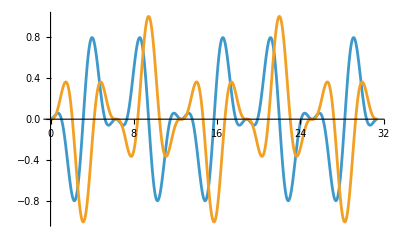

```mathematica
Plot[{v10[t],v01[t]},{t,0,5*2Pi}]
```

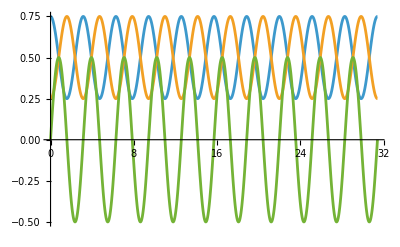

```mathematica
Plot[{v20[t],v02[t],v11[t]},{t,0,5*2Pi}]
```

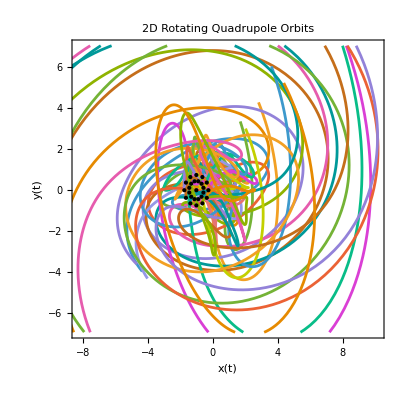

```mathematica
(*2. Construct 2D numerical wavepacket with all 6 scalar coefficient functions*)
obj2DNum=GWP["2D"][{{1,0},{0,1}},{-1,0},{0,1},"Potential"->{"Numerical",v00,v10,v01,v20,v02,v11,0,2*2 Pi}];

(*3. Sample a 2D PolarC ring ensemble*)
xy0Num=GWPEnsemble[obj2DNum,"SamplingMethod"->"PolarC","Grid"->{2,12},"Time"->0];

(*4. Propagate 2D trajectories*)
sol2DNum=EnsembleSolve[xy0Num,Function[{xy,t},Transpose@obj2DNum["VX"][xy[[All,1]],xy[[All,2]],t]],{t,0,2*2 Pi}];

parsed2DNum=EnsembleParse[xy0Num,sol2DNum];
traj2DNum=EnsembleFormat[parsed2DNum,"X0DAT"];

(*5. Plot 2D trajectories and 3D (t,x,y) space-time worldlines*)
worldlines3D=MapThread[Transpose[Prepend[Transpose[#1],#2]]&,{traj2DNum,ConstantArray[parsed2DNum["TDAT"],parsed2DNum["NS"]]}];

GraphicsRow[{ListLinePlot[traj2DNum,AspectRatio->1,Frame->True,FrameLabel->{"x(t)","y(t)"},PlotLabel->"2D Rotating Quadrupole Orbits",Epilog->{PointSize[Small],Black,Point[xy0Num]}],Graphics3D[{Thick,MapIndexed[{ColorData[97,First[#2]],Line[#1]}&,worldlines3D]},Axes->True,AxesLabel->{"t","x","y"},BoxRatios->{2,1,1},PlotLabel->"Space-Time Worldlines (t, x, y)"]},ImageSize->800]
```

```mathematica
Graphics3D[{Thick,MapIndexed[{ColorData[97,First[#2]],Line[#1]}&,worldlines3D]},Axes->True,AxesLabel->{"t","x","y"},BoxRatios->{3,1,1},PlotLabel->"Space-Time Worldlines (t, x, y)"]
```

-Graphics3D-

```mathematica
(*Extract the time grid and trajectory coordinates from parsed2DNum*)
tGrid=parsed2DNum["TDAT"];

Manipulate[Module[{tNow=tGrid[[k]],tailStart=Max[1,k-15]},Show[ContourPlot[Evaluate[obj2DNum["AX"][x,y,tNow]^2],{x,-3.5,3.5},{y,-3.5,3.5},Contours->8,ColorFunction->"DeepSeaColors",PlotRange->All,Exclusions->None],Graphics[{(*Fading comet tails over the last 15 time steps*)White,Opacity[0.7],Thick,Line[traj2DNum[[All,tailStart;;k]]],(*Current particle positions*)Yellow,PointSize[Medium],Point[traj2DNum[[All,k]]]}],Frame->True,FrameLabel->{"x","y"},PlotLabel->Row[{"t = ",NumberForm[tNow,{4,2}]}],ImageSize->420]],{{k,1,"Time Step"},1,Length[tGrid],1,Animator}]
```

```mathematica
(*Initial 2D velocities at t=0*)
vxy0Num=Transpose@obj2DNum["VX"][xy0Num[[All,1]],xy0Num[[All,2]],0];

(*Classical force F_class={-dV/dx,-dV/dy}+Quantum force QFX*)
fTotal2D[xy_,t_]:=Module[{x=xy[[All,1]],y=xy[[All,2]],fxClass,fyClass,qf},fxClass=-v10[t]-2 v20[t] x-v11[t] y;
fyClass=-v01[t]-2 v02[t] y-v11[t] x;
qf=obj2DNum["QFX"][x,y,t];
Transpose[{fxClass+qf[[1]],fyClass+qf[[2]]}]/obj2DNum["MASS"]];

(*Integrate 2nd-order 2D Newton-Bohm equations*)
sol2DNum2nd=EnsembleSolve[xy0Num,vxy0Num,fTotal2D,{t,0,2 Pi}];

(*Maximum 2D endpoint discrepancy between 1st-order and 2nd-order propagation*)
Max@Abs[Through[sol2DNum[2 Pi]]-Through[sol2DNum2nd[2 Pi]]]
```

5.54098×10^-6